# An Introduction to Mathematical Modeling in Ecology and Evolution Sally Otto (2020)

Sponsors:
BIOS2 (NSERC - CREATE Training program)

Resources:
* An Introduction to Mathematical Modeling in Ecology and Evolution (2007) by Otto and Day
* Biomathematical modeling lecture notes (http://www.zoology.ubc.ca/~bio301/Bio301/Lectures.html)
* Mathematica labs (http://www.zoology.ubc.ca/biomath/labs.htm)

## Part 1: Classic one-variable models in ecology and evolution

### Exponential growth

Assumes that each individual replicates at a constant rate over time:

	 n[t+1] = R n[t]		Discrete-time model ("Recursion equation")
	
	 dn/dt=n'[t]= r n[t]		Continuous-time model ("Differential equation")
	
n[t]:	The population size at time t 
R:	The number of offspring per parent in a time unit (from t to t+1).
r:	The growth rate per parent per time unit.

### Logistic growth

Assumes that each individual replicates at a rate that declines as a linear function of the current population size:

	 n[t+1] =(1+r (1-n[t]/K))n[t]				Discrete-time model
	
	dn/dt=n'[t]=r (1-n[t]/K) n[t]					Continuous-time model
	
r:  	The "intrinsic" growth rate per parent per unit time, realized when competition is weak (population size small)
K:  	The "carrying capacity" defined as the population size at which competition causes the population to neither grow nor shrink

### Haploid model of selection

Assumes that each individual carrying A has a fitness of 1+s relative to individuals carrying a, where p is the frequency of A:

	 p[t+1] =((1+s)p[t])/((1+s)p[t]+(1-p[t]))					Discrete-time model
	
	dp/dt=p'[t]=s p[t] (1-p[t])					Continuous-time model
	
p:	Frequency of allele A at a locus with two alleles (a and A).  p must lie between 0 and 1.
s:	Selection coefficient favoring allele A over a.

### Getting used to Mathematica

Mathematica can be used as a sophisticated calculator.

For example, if r = 0.3, K = 100, and n = 90 at some time, what population size do we expect in the next generation given logistic growth?

```mathematica
(1+r (1-n/K))n/.n->90/.r->0.3/.K->100
```

Mathematica can also plot functions.

For example, the per capita number of offspring per parent in the logistic model:

```mathematica
Plot[(1+r (1-n/K))/.r->0.3/.K->100,{n,0,250},PlotRange->{Automatic,{0,1.5}},AxesLabel->{"n","kids"}]
```

```mathematica
Manipulate[Plot[(1+r (1-n/K)),{n,0,250},PlotRange->{Automatic,{0,1.5}}],{{r,0.3},0.01,0.5},{{K,100},10,200}]
```

Or the number of offspring produced by the entire population in the logistic model:

```mathematica
Manipulate[Plot[(1+r (1-n/K))*n,{n,0,250},PlotRange->{Automatic,{0,200}}],{{r,0.3},0.01,0.5},{{K,100},10,200}]
```

The real power of Mathematica, however, is that it can handle commands involving variables and parameters without having to specify their values.

For example, at what population size do we see the largest total number of offspring produced in the logistic model?

```mathematica
D[(1+r (1-n/K))n,n]
```

```mathematica
Solve[%==0,n]
```

#### Question 1: At what speed does an allele rise in frequency?

Using the continuous-time model, plot the rate of change  s p(1-p)as a function of p (between 0 and 1).  Choose whatever numerical value of s you wish.

#### Question 2: When is evolutionary change fastest?

Again, using the continuous-time model, dp/dt=s p[t] (1-p[t]), what value of p maximizes the rate of allele frequency change?  Use D[ ] to find this result analytically, for any possible value of s.

## Part 2: Equilibria and their stability

### Equilibria

DEFINITION:  An equilibrium is a special value of a variable such that if a system starts at that value, it stays there.

RECIPE: We find equilibria by:
	* Setting the variable at one time and the next (n[t + 1] and n[t]) to the same equilibrium value, n̂,	(Discrete-time model)
	* Setting the change in a variable (dn/dt) to zero when started at n̂,					(Continuous-time model)
and then solving for the value(s) of n̂ that satisfy the resulting equations.

E.g., in the logistic model, if the population size at time t is n[t]=n̂, it will remain at this value only if n[t+1]=n̂.
This gives us an equation that we can solve for n̂, by replacing all instances of n with n̂ in  n[t+1] =(1+r (1-n[t]/K))n[t].

```mathematica
Solve[n̂ ==(1+r (1-(n̂)/K))n̂,n̂]
```

```mathematica
Solve[n==(1+r (1-n/K))n,n]
```

NOTE:  We use == instead of = here because we don't want to set n̂ equal to the right-hand side, we want TO TEST when the left and right will be equal.

Similarly, in continuous-time, we determine what value of n̂ causes  dn/dt= r (1-n[t]/K) n[t] to equal zero:

```mathematica
Solve[0==r (1-(n̂)/K)n̂,n̂]
```

#### Question 3: What are the equilibria for the haploid model of selection?

Find p̂ for both the discrete-time and continuous-time models:

	 p[t+1] =((1+s)p[t])/((1+s)p[t]+(1-p[t]))					Discrete-time model
	
	dp/dt=p'[t]=s p[t] (1-p[t])					Continuous-time model
	
First, use Mathematica to solve for p̂ analytically, then carry out the calculations by hand to confirm your answer.

### Stability

A system may or may not move toward a particular equilibrium.

DEFINITION:  An equilibrium is locally stable if a system near the equilibrium approaches it (attracting).  An equilibrium is unstable if a system near the equilibrium moves away from it (repelling).

A local stability analysis determines whether a system that starts near an equilibrium moves toward (stable) or away from it (unstable).

The idea:  We approximate the dynamics of a model near an equilibrium and then determine how it moves.  To do so, we use an incredibly useful approximation tool:  the Taylor Series.

Taylor series:  For any nicely behaved function, f, of a variable, x[t], we can write the function around x̂ as a series of terms, (x[t]-x̂)^i:

```mathematica
Series[f[x[t]],{x[t],x̂,10 }]
```

For example, Sin[x] can be rewritten as the following function around the point 1/2:

```mathematica
Series[Sin[x],{x,1/2,4}]
```

If we are close enough to the point of interest, then (x[t]-x̂)^i will be small, and we can drop terms that we consider to be negligible.

Constant approximation (drops (x[t]-x̂)^i for i > 0):

```mathematica
const=Normal[Series[Sin[x],{x,1/2,0}]]
```

Linear approximation (drops (x[t]-x̂)^i for i > 1):

```mathematica
lin=Normal[Series[Sin[x],{x,1/2,1}]]
```

Quadratic approximation (drops (x[t]-x̂)^i for i > 2):

```mathematica
quad=Normal[Series[Sin[x],{x,1/2,2}]]
```

```mathematica
Plot[{Sin[x],const,lin, quad},{x,0,Pi},PlotRange->{Automatic,{0,1}},PlotStyle->{Automatic,Dashing[0.1],Dashing[0.04],Dashing[0.01]}]
```

In a local stability analysis, we assume that we are near an equilibrium, and use the Taylor series to approximate the recursion or differential equation, f[n], to linear order:

```mathematica
Normal[Series[f[n[t]],{n[t],n̂ ,1}]]
```

f[n̂]+(n[t]-n̂) f'[n̂]

Describing the recursion equation as a function (f), where n[t+1]=f[n[t]], the Taylor series tells us that:

	n[t+1]≈f[n̂]+(n[t]-n̂) f'[n̂]	(note that f'[n̂] is the derivative of f with respect to n, evaluated at n̂: (df/dn)_(n=n̂))
	n[t+1]≈n̂ +(n[t]-n̂) f'[n̂]	(f[n̂]=n̂ because the recursion started at an equilibrium returns the equilibrium)
	(n[t+1]-n̂)≈(n[t]-n̂) f'[n̂]	(moving n̂ to the left)

so the distance to the equilibrium (n[t]-n̂) changes by a factor λ=f'[n̂] each generation.

Describing the differential equation as a function (f), where dn/dt=f[n[t]], the Taylor series tells us that:

	dn/dt≈f[n̂]+(n[t]-n̂) f'[n̂]
	dn/dt≈0 +(n[t]-n̂) f'[n̂]		(f[n̂]=0 because there is no change at an equilibrium)
	(d(n[t]-n̂))/dt≈(n[t]-n̂) f'[n̂]		(because (d(n[t]-n̂))/dt=(d(n[t]))/dt-(d(n̂))/dt= (d(n[t]))/dt-0)

so the distance to the equilibrium changes at a rate r=f'[n̂].

RECIPE: To determine the stability of an equilibrium:
	* Take the derivative of the recursion equation with respect to the variable, df/dn, and evaluate at an equilibrium λ=(df/dn)_(n=n̂).
		→  The equilibrium is stable only if -1<λ<1						(Discrete-time model)
			If 1<λ, equilibrium is unstable with exponential growth away from it
			If 0<λ<1, equilibrium is stable with exponential growth toward it
			If -1<λ<0, equilibrium is stable with damped oscillations toward it
			If λ<-1, equilibrium is unstable with growing oscillations away from it
 	* Take the derivative of the differential equation with respect to the variable, df/dn, and evaluate at an equilibrium r=(df/dn)_(n=n̂).
		→  The equilibrium is stable only if r < 0						(Continuous-time model)
			If 0<r, equilibrium is unstable with exponential growth away from it
			If r<0, equilibrium is stable with exponential growth toward it

Repeat for each equilibrium of interest.

For example, consider the logistic model in discrete time.  When will the system approach n̂ = 0, causing the system to go extinct?

```mathematica
derivative=D[(1+r (1-n[t]/K))n[t],n[t]]
```

```mathematica
λ=derivative/.n[t]->0
```

For λ to lie between -1 and +1, r must lie between -2 and 0.  [Technically, because 1+r measures the number of offspring per parent when competition is weak, r cannot fall below -1 or it becomes biologically meaningless.]

When will the system approach n̂ = K, causing the system to remain stably at carrying capacity?

```mathematica
λ=derivative/.n[t]->K
```

This will be greater than one if:	r<0		n̂=K is an unstable equilibrium
This will be between 0 and 1 if:	0<r<1		n̂=K is a stable equilibrium
This will be between -1 and 0 if:	1<r<2		n̂=K is a stable equilibrium with damped oscillations
This will be less than -1 if:		r>2		n̂=K is an unstable equilibrium with growing oscillations

#### Question 4: What determines stability of the equilibria for the haploid model of selection?

Under what conditions is p̂=0 stable?

Under what conditions is p̂=1 stable?

You can use either the discrete-time or the continuous-time model:

	 p[t+1] =((1+s)p[t])/((1+s)p[t]+(1-p[t]))					Discrete-time model
	
	dp/dt=p'[t]=s p[t] (1-p[t])					Continuous-time model

Note that, in the discrete-time model, the fitness of A individuals is 1+s times greater than the fitness of a individuals, where 1+s must be positive (fitness can't be negative).

## Part 3: Beyond equilibria

### General solutions

Some models can be solved generally, allowing us to predict the future state at any time in the future and how this depends on the parameters.

DEFINITION:  A general solution describes the state of a system at any future point in time.

There are many methods for finding general solutions (see Chapters 6 & 9), including iterating recursions to deduce a general rule and using recipes to solve differential equations (e.g., separation of variables).

Mathematica makes it easy to find general solutions for many of the simpler models.

Recursion equations:

```mathematica
RSolve[{n[t+1] == R*n[t],n[0]==n0},n[t],t]
```

NOTE:  Again, we use == instead of = here because we don't want to set n[t+1] equal to the right-hand side, we want TO TEST when the left and right will be equal.

```mathematica
RSolve[{p[t+1] ==((1+s)p[t])/((1+s)p[t]+(1-p[t])),p[0]==p0},p[t],t]
```

Differential equations:

```mathematica
DSolve[{D[n[t],t] == R*n[t],n[0]==n0},n[t],t]
```

```mathematica
DSolve[{D[p[t],t] ==s p[t](1-p[t]),p[0]==p0},p[t],t]
```

These can then be used to predict where the system will be:

```mathematica
Manipulate[Plot[(ⅇ^(s t) p0)/(1-p0+ⅇ^(s t) p0),{t,0,100},PlotRange->{Automatic,{0,1}}],{{s,0.1},-0.2,0.2},{{p0,0.05},0.01,0.99}]
```

#### Question 5: Show that the logistic model in discrete time does not have a solution, but the model in continuous time does and then plot this solution.

Use: 

	 n[t+1] =(1+r (1-n[t]/K))n[t]				Discrete-time model
	
	dn/dt=n'[t]=r (1-n[t]/K) n[t]					Continuous-time model

### Simulations

Some models, however, are too complicated to solve.  Some cannot be solved (e.g., the logistic in discrete time), while others may not be worth the time needed to obtain a general solution when all that is needed are solutions to specific cases.

DEFINITION:  A simulation explores a model using specific parameter values and initial states by applying the model's equations repeatedly.

```mathematica
Clear[logistic]
logistic[r_,K_,n0_,t_]:=logistic[r,K,n0,t]=
Block[{n=logistic[r,K,n0,t-1]},
	n+r n (1-n/K)
	]

logistic[r_,K_,n0_,0]=n0
```

n0

Some notes:  
	* Block keeps a set of calculations together, defining local variables in the first {}.  The output will be the last entry of the Block.
	* := sets the left to the right-hand side only after being called and remembers this value.
	* We have to set a starting point or else the system will end up in an infinite loop going backwards in time.

We can then make a table of population sizes:

```mathematica
Table[logistic[1.5,100,10,t],{t,0,100}]
```

and plot this list:

```mathematica
ListPlot[Table[logistic[1.5,100,10,t],{t,0,100}],PlotRange->{{0,100},{0,140}},Joined->True]
```

For r values between 0 and 2, we see a stable equilibrium, as we would expect from the local stability analysis of n̂=k.  For 2<r, we see oscillations, for 2.58<r, chaotic dynamics are observed, while for 3<r the system is driven extinct.

#### Question 6: Simulating extinction

Add an If[ ] statement to the above simulation to return zero if ever the population size is predicted to be negative.

Use this simulation to explore what happens with r = 3.01 (generate a table as above, and ListPlot it).

### Numerical solutions

Differential equations can also be solved numerically using Mathematica's NDSolve routines, which can work even for models that cannot be solved analytically.

```mathematica
logisticD[r_,K_,n0_]:=NDSolve[{D[n[t],t]==r (1-n[t]/K) n[t],n[0]==n0},n[t],{t,0,100}]
```

```mathematica
logisticD[0.5,100,10]
```

Some notes:  
	* We must use := here because we don't want the routine to start calculating until we call it with specific values of the parameters.
	* The code is very similar to DSolve, except that we must specify the time frame over which we want a solution (here 0-100)
	* When we do call the function, Mathematica tells us that it has represented the solution as a function, which we can interrogate.

We can then evaluate this function at specific values or in a plot:

```mathematica
Evaluate[logisticD[0.1,100,10]/.t->20]
```

```mathematica
Plot[Evaluate[(n[t]/.logisticD[0.1,100,10])],{t,0,100}]
```

## Part 4: Example of building a model from scratch

Scenario:  Let's model the number of species on a large landmass over long periods of evolutionary time, where the number of species is primarily influenced by speciation and extinction events within the landmass.  If extinction risk, d, is constant per species but speciation rate declines from an initial value, b, exponentially with the number of species already present (because of competition for overlapping resources/niches), then develop a model that might describe the number of species, n, on the landmass.

## Part 5: Extending to models with more than one variable

The above models were all in one variable (e.g., the population size or the allele frequency).  Fortunately, the ideas are the same (but the methods more cumbersome) with models involving more than one variable.  As an example, let's work with a model of an alternation of generations between haploids and diploids.

Alternation of generations is a life history common to many algae, in which both the haploid and the diploid phases exist as independently growing and reproducing organisms.

Haploid individuals (gametophytes) produce diploid individuals by producing haploid gametes that then unite.

Diploid individuals (sporophytes) produce haploid individuals by meiosis.

During a year, we assume that parents reproduce and then die, where:

	a = the number of diploid offspring produced per haploid parent
	b = the number of haploid offspring produced per diploid parent
	
Then, if h[t] represents the number of haploid individuals and d[t] the number of diploid individuals, we can track the size of both populations over time using discrete-time recursions:

Haploids:  	h[t+1] = b d[t]
Diploids:	d[t+1] = a h[t]

We can describe analogous procedures for continuous-time models, but to keep matters simple, we'll focus here only on discrete-time models

### Equilibria

An equilibrium is defined in the same way, as a special point at which the system stays if started there.  The only trick is to make sure that all of the variables remain constant.

For the model of alternating generations:

```mathematica
Solve[{ĥ ==b d̂,d̂ ==a ĥ},{ĥ,d̂}]
```

Here we've asked Mathematica for all of the sets of solutions for the number of haploids and diploids {ĥ,d̂} that cause both of these values to remain constant in the next generation.  The answer is that there's only one equilibrium point, with neither haploids or diploids.

### Stability

To determine stability, we need to have a multi-dimensional analogue of λ that describes the factor by which the distance from the equilibrium grows each generation.

Idea:  We again approximate the recursions near an equilibrium point using the Taylor series, but we do this for each recursion equation and each variable.  For example, if we have two recursion equations, f and g, describing changes in two variables, n and m, we could apply the Taylor series as before and rearrange the results as:

		(n[t+1]-n̂)=(n[t]-n̂) (df/dn)_(n̂,m̂)+(m[t]-m̂) (df/dm)_(n̂,m̂)	
		(m[t+1]-m̂)=(n[t]-n̂) (dg/dn)_(n̂,m̂)+(m[t]-m̂) (dg/dm)_(n̂,m̂)	
  
Book-keeping is easier, however, and we can use the power of matrix algebra, if we write this in matrix form:

		distance to equilibrium in next generation 	= stability matrix times distance to equilibrium in previous generation
		
				(n[t+1]-n̂
m[t+1]-m̂)  		=  (df/dn | df/dm
dg/dn | dg/dm)_(n̂,m̂)(n[t]-n̂
m[t]-m̂) 
				
But how do we tell if this matrix shrinks the distance or expands the distance?

DEFINITION: A matrix involving d variables has d eigenvalues that describe the factor by which the system grows along different directions (called eigenvectors).  The leading eigenvalue, λ, of a matrix is the largest in magnitude of these eigenvalues, and it predicts whether the matrix stretches (|λ| > 1) or shrinks (|λ| < 1) a vector that it multiplies.  If λ is a complex number, the system will cycle.

CAUTION:  When calculating the stability matrix, decide on an order for the variables and then take the derivative of the recursion for the first variable in the first row with respect to the first variable in the first column.  Keep the order of the variables the same for all subsequent rows and columns.

For example, take the two recursion equations for the haploid-diploid model:

```mathematica
eqnh=b d[t];
eqnd=a h[t];
```

The first equation gives us h[t+1], so we must take the derivatives first with respect to h[t] and then d[t], and then evaluate at the equilibrium of interest (here 0,0):

```mathematica
matrix={{D[eqnh,h[t]],D[eqnh,d[t]]},
{D[eqnd,h[t]],D[eqnd,d[t]]}}/.{h[t]->0,d[t]->0}
```

The eigenvalues of which are:

```mathematica
Eigenvalues[%]
```

Because a and b describe the number of offspring, these eigenvalues must be positive.  The magnitude of these two eigenvalues is the same, |λ| = √(a b), which tells us that the system will move away from the equilibrium at {0,0} only if √(a b)>1, which implies that the product of a and b must be greater than one.

	→  A haploid-diploid species can grow in size even if one phase produces less than
	a replacement number of offspring (e.g., a < 1), as long as the other phase compensates (e.g., b > 1).

### Simulation

We can use the same basic code as with the logistic model to track the size of the haploid and diploid populations.  The only difference is that the result is now a vector {h,d}, whose first part is the number of haploids and whose second part is the number of diploids.

```mathematica
Clear[hapdip]
hapdip[a_,b_,h0_,d0_,t_]:=hapdip[a,b,h0,d0,t]=
Block[{h=Part[hapdip[a,b,h0,d0,t-1],1],d=Part[hapdip[a,b,h0,d0,t-1],2]},
	{b d,a h}
	]

hapdip[a_,b_,h0_,d0_,0]:={h0,d0}
```

Some notes:  
	* Block keeps a set of calculations together, defining local variables in the first {}.  The output will be the last entry of the Block.
	* := sets the left to the right-hand side only after being called and remembers this value.
	* We have to set a starting point or else the system will end up in an infinite loop going backwards in time.

We can then make a table of population sizes for {haploids, diploids}:

```mathematica
Table[hapdip[0.7,1.5,10,10,t],{t,0,100}]
```

or plotting haploids in red and diploids in blue:

```mathematica
ListPlot[{Table[Part[hapdip[0.7,1.5,10,10,t],1],{t,0,100}],Table[Part[hapdip[0.7,1.5,10,10,t],2],{t,0,100}]},Joined->True,PlotStyle->{Red,Blue}]
```

Notice that in this case the diploids have higher reproductive capacity (1.5 offspring on average), yet it is the haploid population size that grows to a larger size.  This is, of course, because diploids beget haploids.

### A case with complex eigenvalues [EXTRA]

Some systems cycle over time.  As an example, let's consider the classic predator-prey model.

Let H[t] represent the numbers of prey and P[t] represent the numbers of predators.  The prey are assumed to grow exponentially, but they are
captured by predators at a rate that depends on both the availability of prey and predators.

The discrete-time recursions are thus:

Prey:  		H[t+1] = H[t] + r H[t] - b H[t] P[t]
Predator:	P[t+1] = P[t] + c H[t] P[t] - d P[t]

which uses the following parameters:
	the growth rate of the prey in the absence of the predator (r),
	the capture rate at which predators contact and kill prey (b),
	the rate at which eaten prey are turned into predator babies (c),
	and the death rate of predators (d).

Question 7:  What are the equilibria of this model?

```mathematica
Solve[{...},{Ĥ,P̂}]
```

Here we've asked Mathematica for all of the sets of solutions for the number of prey and predators {Ĥ,P̂}that cause both of these values to remain constant in the next generation.

Question 8:  Under what conditions is the equilibrium with both species present stable?

```mathematica
eqn1=H[t] + r H[t] - b H[t] P[t];
eqn2 = P[t] + c H[t] P[t] - d P[t];
```

```mathematica
matrix={...}
```

Let's consider the stability of the equilibrium with both prey and predators present:

```mathematica
matrix/.{H[t]->...,P[t]->...}
```

```mathematica
Eigenvalues[%]
```

The answer will involve a complex number, where ⅈ=√-1.  The above eigenvalues can be written more simply as {1+ⅈ √(d r),1-ⅈ √(d r)}.  Note that the death rate of predators (d) and the intrinsic growth rate of prey (r) can be assumed to be positive in this model, so these eigenvalues are complex numbers.

The recipe for discrete-time models remains the same:  we find the absolute magnitude of the eigenvalue, |λ|, and if it is greater than one then the system is unstable.  (The rule is slightly different for continuous-time models.  See Chapter 8.)

DEFINITION: The absolute magnitude of a complex number is |λ|=√((real part)^2+(complex part)^2).

Here, the real part is "1" and the complex part is the part "√(d r)" multiplying ⅈ=√-1.  So the magnitude of both eigenvalues is √((1)^2+(√(d r))^2), or just √(1+d r), which must be a number greater than one.

→  The predator-prey model will cycle (because λ is complex) and expand away 
	from the equilibrium at {H[t]→d/c,P[t]→r/b} (because |λ| > 1).

We can use the same basic code again to track the prey and predator population sizes.

```mathematica
predprey[r_,b_,c_,d_,H0_,P0_,t_]:=predprey[r,b,c,d,H0,P0,t]=
Block[{H=Part[predprey[r,b,c,d,H0,P0,t-1],1],P=Part[predprey[r,b,c,d,H0,P0,t-1],2]},
	{H + r H - b H P, P+ c H P - d P}
	]

predprey[r_,b_,c_,d_,H0_,P0_,0]:={H0,P0}
```

We can then make a table of population sizes for {prey, predators}:

```mathematica
Table[predprey[0.7,0.01,0.0001,0.1,900,70,t],{t,0,100}]
```

or plotting prey in red and predators in blue:

```mathematica
ListPlot[{Table[Part[predprey[0.7,0.01,0.0001,0.1,900,70,t],1],{t,0,100}],Table[Part[predprey[0.7,0.01,0.0001,0.1,900,70,t],2],{t,0,100}]},Joined->True,PlotStyle->{Red,Blue},PlotRange->All]
```

I purposely started this near the equilibrium (1000,70), otherwise it cycles out so fast that it crashes and burns very quickly.  Even here, the prey go extinct by the end of this 100-generation simulation.

We can also present this graph as a phase-diagram, where the number of predators (y-axis) is plotted against the number of prey (x-axis):

```mathematica
ListPlot[Table[{Part[predprey[0.7,0.01,0.0001,0.1,900,70,t],2],Part[predprey[0.7,0.01,0.0001,0.1,900,70,t],1]},{t,0,100}],Joined->True,PlotStyle->{Red,Blue},PlotRange->All,AxesOrigin->{0,0}]
```

### Accounting for randomness [EXTRA]

In all of the above models, we've assumed that the state of the system can be precisely predicted in the next time step.  Such models are called "deterministic".  In natural systems, there is always a degree of randomness or stochasticity to life.  For example, even if the average number of offspring per parent were 2.3, the actual number will be an integer (0,1,2,3...).   

The offspring number might, for instance, represent a random draw of the Poisson distribution with a certain mean (here 2.3):

```mathematica
RandomInteger[PoissonDistribution[2.3]]
```

We can incorporate such randomness (called "demographic stochasticity") into the above ecological models by having the number of offspring be drawn from a Poisson:

```mathematica
Clear[hapdip]
hapdip[a_,b_,h0_,d0_,t_]:=hapdip[a,b,h0,d0,t]=
Block[{h=Part[hapdip[a,b,h0,d0,t-1],1],d=Part[hapdip[a,b,h0,d0,t-1],2]},
numhap=If[b d>0,RandomInteger[PoissonDistribution[b d]],0];
numdip=If[a h >0,RandomInteger[PoissonDistribution[a h]],0];
{numhap,numdip}
	]

hapdip[a_,b_,h0_,d0_,0]:={h0,d0}
```

Some notes:  
	* Block keeps a set of calculations together, defining local variables in the first {}.  The output will be the last entry of the Block.
	* := sets the left to the right-hand side only after being called and remembers this value.
	* We have to set a starting point or else the system will end up in an infinite loop going backwards in time.
	* The Poisson distribution can be evaluated by Mathematica only if the expected number is positive.  This will cause problems if the population ever goes extinct (expectation is zero).  The If statements says to draw a random number from the Poisson only if the expected number is positive.

We can then make a table of population sizes for {haploids, diploids}:

```mathematica
Table[hapdip[0.7,1.5,10,10,t],{t,0,100}]
```

or plotting haploids in red and diploids in blue:

```mathematica
ListPlot[{Table[Part[hapdip[0.7,1.5,10,10,t],1],{t,0,100}],Table[Part[hapdip[0.7,1.5,10,10,t],2],{t,0,100}]},Joined->True,PlotStyle->{Red,Blue}]
```

Reenter this sub-directory a few times to see how the plots change due to demographic stochasticity.  Occassionally, you'll see the whole population go extinct, despite the fact that we expect it to grow with a = 0.7 and b = 1.5.

To learn more about probability theory and stochastic models (both analytical and simulation-based methods), read Primer 3 and Chapters 13-15.

## Part 6: Another example of building a model from scratch

Scenario:  Consider two types of individuals that can help one another to raise a brood (e.g., one type might be better at detecting predators and the other type at collecting food).  Assume that neither of the two types would be able to grow on their own, with the number of offspring per parent, 1-r1 and 1-r2, respectively, being less than one.  Through cooperation, however, the per capita growth of each type rises linearly with the number of the other type, with slopes ρ1 and ρ2.

## Appendix: Quick reference to Mathematica

### Getting started

```mathematica
Help -> Documentation Center   - Can be used to search for commands of interest

?Command   - gives a fairly detailed description of a command, e.g., ?Plot tells you all about this command.  
	You can use * as a wildcard, for instance ?*Plot* gives a list of all commands with Plot in their name. 
	More help can be found in the menu under "Help", in the Function Navigator or Documentation Center.
	
*   - Times command (2*3 gives 6).  Spaces can also be used but be careful (e.g, a=2 3 gives six
	but a=23 gives twenty-three)

^   - Power command (2^3 gives 8)

n!  - factorial (3! gives 6)

{}  - denotes a list, e.g., {2,3,4}

()  - Places variables together, e.g., (1+x)/(1-x) takes 1+x over 1-x

[]  - Generally used to denote that something is a function of something else

%# - grabs previous output number #.

%  - grabs the previous line of output regardless of the number

%% - grabs output two lines back.  Note: naming outputs is safer (see next section).

f /. object1 -> object2  
           - tells Mathematica to make replace object1 with object2 in the function
          e.g.,  3*x^2 /. x -> 2*y+z gives  3*(2*y + z)^2
```

### Avoiding conflict with Mathematica

Mathematica tends to use capital letters for its functions, so its often a good idea to use 
lower case names for your functions and variables.

If you refer to previous entries using %, it can be difficult to know exactly what your 
previous entry was.  It is safer to assign a name to the output and then refer to this name later.

For example,

```mathematica
myderivative = D[a Sin[b x], x]
```

```mathematica
Plot[myderivative/.a->1/.b->3,{x,0,10}]
```

### Functions and constants in Mathematica (A small fraction!)

Abs[x]  - Takes the absolute value of x

E   - The exponential constant 2.71838.  E^(x) can be invoked using Exp[x]

I   - The square root of negative 1.

Infinity   - Self-explanatory.

Log[x]   -Takes the natural log of x

Log[b,x]   -Takes the log of x in base b

Pi   - 3.14159...

Sin[x], Cos[x], Tan[x]   - trigonometric functions
ArcSin[x], ArcCos[x], ArcTan[x] -  inverse trigonometric functions

Sqrt[x]   - Square root

### Writing equations in Mathematica

```mathematica
x=y   - Sets x to y immediately and from then on (use Clear[x] to unassign x), e.g., plot1=Plot[x^2,{x,0,10}]

x:=y   - Does nothing until x is called, at which point x is assigned the value y

x==y    - Tests whether x equals y BUT makes no assignment

f[x_]:=  - This is how you define a function (called "f") of x, e.g., f[x_] := x^2

f[x] - This gives the function evaluated at x, e.g., f[3] gives 9 in the above example

f[x_,y_,...]=  - This is how you define a function of several variables
```

### A list of helpful commands

Clear[symbol1,symbol2,...] - clears variable or function definitions, 
	e.g., Clear[x, y, pop1]

Clear[“Global`*”] - clears all variable or function definitions from memory

Collect[eqn,{terms},Factor] - collects parts of an equation involving “terms” and 
	factors them separately (if only one “term”, the braces aren’t needed)
	e.g. Collect[a-b+a x-2 b x+a^2 x^2+2 a b x^2+b^2 x^2, x, Factor]

D[f,x]   - takes the partial derivative of f with respect to x - e.g. D[x^2+y Log[x], x]

D[f, {x, n}]   - takes the nth derivative with respect to x - e.g.  D[x^2+y Log[x],{x,2}]

DSolve[eqn, y[x],x]   - solves differential equation for y as a function of x 
	(SYMBOLICALLY) e.g. DSolve[{y'[x] == k y[x], y[0]==y0, y[x],x]

DSolve[eqns, {y1,y2,y3,..}, x] same as above but for a system of eqns 
	e.g. pred-prey equations DSolve[{y'[x] == k y-x, z'[x]==x+z}, {y[x],z[x]}, x]

NDSolve[eqns, y, {x, xmin,xmax}] - same as DSolve but seeks solution
	NUMERICALLY - e.g. NDSolve[{y'[x] ==4 y[x], y[3]==62}, y[x], {x, 0,20}]

Expand[expr]- expands an expr e.g. Expand[(1+x)^2] gives 1+2x+x^2

Evaluate[object] - evaluates a symbolic object like interpolating functions

Factor[polynomial] - self explanatory - e.g. Factor[x^2 + 2 x + 1]

FindRoot[eqn1==eqn2, {x, x0}] - searches for numerical root of eqn1==eqn2
            starting at x0 e.g. FindRoot[Log[x] + x + Arctan[x] == 0, {x, 4}] tries to find 
            x that satisfies this very ugly - impossible to solve by hand equation, starting at x=4.

For[start,test,increment,body] - repeats procedure “body”, starting from “start”  
	until the “test” condition is met, adding “increment” each time, 
	e.g., For[i=1, i≤10, i=i+1, Print[i]] prints out integers 1 through 10.

Integrate[f,x] - finds indefinite integral of f with respect to x 
	e.g., Integrate[Log[x], x]

Integrate[f, {x, xmin, xmax}] - computes definite integral from xmin to xmax
	e.g., Integrate[Log[x], {x, 1,6}]

ListPlot[list] - plots a list of integers, e.g., ListPlot[{2,4,3,5,4}]

ListPlot[{{x1, y1},{x2, y2},...}] - plots a series of {x, y} values,
	e.g., ListPlot[{{1,2},{2,1},{5,7}}] To join the points with a line use:
	 ListPlot[{{1,2},{2,1},{5,7}},PlotJoined->True] (in Mathematica 5)
	 ListPlot[{{1,2},{2,1},{5,7}},Joined->True] (in more recent versions)

N[f] - gives a numerical value for an expression - e.g. N[Pi] gives 3.14159

Part[eqn,i] - grabs  the ith part of eqn, e.g., Part[3x^2+x^3,2] gives x^3

Plot[f,{x,xmin,xmax}] - plots f versus x on the interval [xmin,xmax] 
            e.g., Plot[x^2, {x,0,2}]   NOTE: Plot has lots of options e.g. AxesLabel,
            Grid, AxesOrigin, etc. See the manual for a complete list and usage 
            e.g.,  Plot[x^2, {x,0,2}, PlotStyle->Dashed] makes a dashed curve.

Plot3D[f, {x, xmin, xmax}, {y, ymin, ymax}] - makes a 3D plot of f

Show[graphics, options] - displays graphic objects using options e.g. 
	Show[popplot1, PlotJoined->True]

Simplify[expr] - does its best to simplify an expression, expr

Solve[eqns, vars] - tries to solve one or a system equations for the vars specified 
	(SYMBOLICALLY)- e.g. Solve[{x+y ==1, x-y ==4}, {x,y}]

NSolve[eqns, vars] - does the same thing as  Solve, but does it NUMERICALLY
	(See also FindRoot)

Sum[f, {i, imin, imax}] - sums  f from i to imax i.e. f[1] + f[2] + f[3] + ... 
            (only really interesting if f depends on i) - e.g. Sum[i, {i, 1,4}] gives 10.
            
Reduce[{eqns}] - can be used to determine if a statement is true or false 
	e.g., Reduce[{a + b > 1, a < 0, b < 0}]
	
RSolve[eqns, vars] - solves a discrete-time equation for y as a function of x 
	(SYMBOLICALLY) e.g. RSolve[{n[t+1] == R n[t], n[0]==n0}, n[t],t]
	
Table[f, {i, imin, imax}]- makes a table in list format of the function f
	with i values that run from imin to imax - e.g. Table[i, {i, 1,4}] gives {1,2,3,4}.

### Libraries

Mathematica has some libraries or packages that it does not load automatically.
The Documentation Center will tell you if a function needs a library.
For example, to plot error bars on a list plot, you will need:

```mathematica
Needs["ErrorBarPlots`"]
```

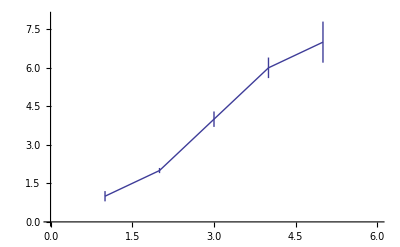

```mathematica
ErrorListPlot[{{{1,1},ErrorBar[0.2]},{{2,2},ErrorBar[0.1]},{{3,4},ErrorBar[0.3]},{{4,6},ErrorBar[0.4]},{{5,7},ErrorBar[0.8]}}, Joined->True,PlotRange->{{0,6},{0,8}}]
```